# Figure 2

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### Data

```mathematica
data1=Import["Data/fidelities_kappa0_1.dat"];
data2=Import["Data/qfi_kappa0_1.dat"];
data3=Import["Data/negativity_kappa0_1.dat"];
data1b=Import["Data/fidelities_kappa_1.dat"];
data2b=Import["Data/qfi_kappa_1.dat"];
data3b=Import["Data/negativity_kappa_1.dat"];
data4=Import["Data/fidelities_kappa0_2.dat"];
data5=Import["Data/qfi_kappa0_2.dat"];
data6=Import["Data/negativity_kappa0_2.dat"];
data4b=Import["Data/fidelities_kappa_2.dat"];
data5b=Import["Data/qfi_kappa_2.dat"];
data6b=Import["Data/negativity_kappa_2.dat"];
```

```mathematica
NC=80;
τ=4.29;
dat1 =Table[{data1[[i,1]]/τ,data1[[i,3]]},{i,2,Length[data1]}];
dat2 =Table[{data1[[i,1]]/τ,data1[[i,2]]},{i,2,Length[data1]}];
dat3=Table[{data2[[i,1]]/τ,data2[[i,2]]-data2[[1,2]]},{i,1,Length[data2]}];
dat4 =Table[{data2[[i,1]]/τ,data2[[i,3]]-data2[[1,3]]},{i,1,Length[data2]}];
dat3gr=Table[{data2[[i,1]]/τ,data2[[i,5]]-data2[[1,5]]},{i,1,Length[data2]}];
dat4gr =Table[{data2[[i,1]]/τ,data2[[i,6]]-data2[[1,6]]},{i,1,Length[data2]}];
dat5 =Table[{data3[[i,1]]/τ,2*data3[[i,3]]},{i,1,Length[data3]}];
dat6 =Table[{data3[[i,1]]/τ,data3[[i,4]]},{i,1,Length[data3]}];
dat7 =Table[{data1[[i,1]]/τ,data1[[i,4]]},{i,2,Length[data1]}];
dat1b =Table[{data1b[[i,1]]/τ,data1b[[i,3]]},{i,2,Length[data1b]}];
dat2b =Table[{data1b[[i,1]]/τ,data1b[[i,2]]},{i,2,Length[data1b]}];
dat3b=Table[{data2b[[i,1]]/τ,data2b[[i,2]]-data2b[[1,2]]},{i,1,Length[data2b]}];
dat4b =Table[{data2b[[i,1]]/τ,data2b[[i,3]]-data2b[[1,3]]},{i,1,Length[data2b]}];
dat3grb=Table[{data2b[[i,1]]/τ,data2b[[i,5]]-data2b[[1,5]]},{i,1,Length[data2b]}];
dat4grb =Table[{data2b[[i,1]]/τ,data2b[[i,6]]-data2b[[1,6]]},{i,1,Length[data2b]}];
dat5b =Table[{data3b[[i,1]]/τ,2*data3b[[i,3]]},{i,1,Length[data3b]}];
dat6b =Table[{data3b[[i,1]]/τ,data3b[[i,4]]},{i,1,Length[data3b]}];
dat7b =Table[{data1b[[i,1]]/τ,data1b[[i,4]]},{i,2,Length[data1b]}];
τ2=8.2;
dat8 =Table[{data4[[i,1]]/τ2,data4[[i,3]]},{i,2,Length[data4]}];
dat9 =Table[{data4[[i,1]]/τ2,data4[[i,2]]},{i,2,Length[data4]}];
dat10=Table[{data5[[i,1]]/τ2,data5[[i,2]]-data2[[1,2]]},{i,1,Length[data5]}];
dat11 =Table[{data5[[i,1]]/τ2,data5[[i,3]]-data2[[1,3]]},{i,1,Length[data5]}];
dat10gr=Table[{data5[[i,1]]/τ2,data5[[i,5]]-data2[[1,5]]},{i,1,Length[data5]}];
dat11gr =Table[{data5[[i,1]]/τ2,data5[[i,6]]-data2[[1,6]]},{i,1,Length[data5]}];
dat12 =Table[{data6[[i,1]]/τ2,2*data6[[i,3]]},{i,1,Length[data6]}];
dat13 =Table[{data6[[i,1]]/τ2,data6[[i,4]]},{i,1,Length[data6]}];
dat14 =Table[{data6[[i,1]]/τ2,data4[[i,4]]},{i,2,Length[data4]}];
dat8b =Table[{data4b[[i,1]]/τ2,data4b[[i,3]]},{i,2,Length[data4b]}];
dat9b =Table[{data4b[[i,1]]/τ2,data4b[[i,2]]},{i,2,Length[data4b]}];
dat10b=Table[{data5b[[i,1]]/τ2,data5b[[i,2]]-data2b[[1,2]]},{i,1,Length[data5b]}];
dat11b =Table[{data5b[[i,1]]/τ2,data5b[[i,3]]-data2b[[1,3]]},{i,1,Length[data5b]}];
dat10grb=Table[{data5b[[i,1]]/τ2,data5b[[i,5]]-data2b[[1,5]]},{i,1,Length[data5b]}];
dat11grb =Table[{data5b[[i,1]]/τ2,data5b[[i,6]]-data2b[[1,6]]},{i,1,Length[data5b]}];
dat12b =Table[{data6b[[i,1]]/τ2,2*data6b[[i,3]]},{i,1,Length[data6b]}];
dat13b =Table[{data6b[[i,1]]/τ2,data6b[[i,4]]},{i,1,Length[data6b]}];
dat14b =Table[{data6b[[i,1]]/τ2,data4b[[i,4]]},{i,2,Length[data4b]}];
```

#### i) a (Fidelities)

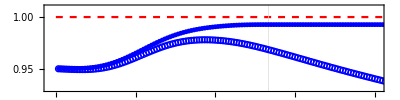

```mathematica
Show[ListPlot[{dat1,dat1b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"○",6},{"◇",6},{"◇",6}},PlotLegends->Placed[{"",""},{0.04,0.52}],PlotRange->{{-2,NC+41},{0.93,1.01}},GridLines->{{NC},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[1,{x,0,1100},PlotStyle->{Red,Dashed}],AspectRatio->0.25]
```

#### ii) a (Phase sensitivity)

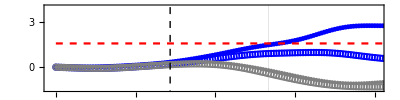

```mathematica
Show[ListPlot[{dat3,dat3b},Joined->False,
PlotStyle->{Blue,Blue,Gray},PlotMarkers->{{"●",5},{"○",6},{"○",6}},PlotRange->{{-2,NC+41},{-1.5,4}},GridLines->{{NC},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],ListPlot[{dat3gr},PlotStyle->Gray,PlotMarkers->{"●",3.8},PlotLegends->Placed[{""},{0.05,0.43}]],ListPlot[{dat3grb},PlotStyle->Gray,PlotMarkers->{"○",6},PlotLegends->Placed[{""},{0.05,0.12}]],Plot[3.3962900879605664-1.828343796849751,{x,0,1100},PlotStyle->{Red,Dashed}],Plot[10-1.828343796849751,{x,0,1100},PlotStyle->{Gray,Dashed}],Epilog->{Dashed,Black,Line[{{43,-2},{43,10}}],Line[{{105,-2},{1000,10}}]},AspectRatio->0.25]
```

#### iii) a (Negativity)

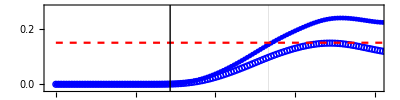

```mathematica
Show[ListPlot[{dat5,dat5b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"◇",6}},PlotRange->{{-2,NC+41},{-0.02,0.28}},GridLines->{{NC},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}](*,Plot[0,{x,0,1100},PlotStyle->{Black,Dashed}]*),Plot[0.1499,{x,0,1100},PlotStyle->{Red,Dashed}],Epilog->{Black,Line[{{43,-1},{43,1.5}}]},AspectRatio->0.25]
```

#### iv) a (Chi)

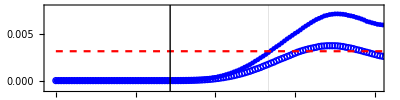

```mathematica
Show[ListPlot[{dat6,dat6b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"◇",6}},PlotRange->{{-2,NC+41},{-0.001,0.008}},GridLines->{{NC},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}](*,Plot[0,{x,0,1100},PlotStyle->{Black,Dashed}]*),Plot[0.003177,{x,0,1100},PlotStyle->{Red,Dashed}],Epilog->{Black,Line[{{43,-1},{43,1}}]},AspectRatio->0.25]
```

#### v) a (Negativity Correlation)

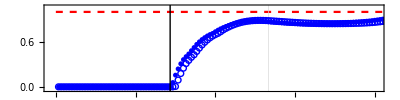

```mathematica
Show[ListPlot[{dat7,dat7b},Joined->False,
PlotStyle->{Blue,Blue,Blue,Darker[Green],Blue,Darker[Green]},PlotMarkers->{{"●",5},{"○",6},{"○",6},{"◇",6},{"◇",6}},PlotRange->{{-2,NC+41},{-0.04,1.07}},GridLines->{{NC},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[1,{x,0,1100},PlotStyle->{Red,Dashed}],Epilog->{Black,Line[{{43,-2},{43,2}}]}(*,Plot[0.9212480350262198,{x,0,1100},PlotStyle->{Black,Dashed}]*),AspectRatio->0.25]
```

#### i) b (Fidelities)

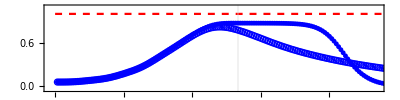

```mathematica
Show[ListPlot[{dat8,dat8b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"○",6},{"◇",6},{"◇",6}},PlotLegends->Placed[{"",""},{0.05,0.5}],PlotRange->{{-2,NC+61},{-0.05,1.1}},GridLines->{{NC},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[1,{x,0,1100},PlotStyle->{Red,Dashed}](*,Plot[0.9212480350262198,{x,0,1100},PlotStyle->{Black,Dashed}]*),AspectRatio->0.25]
```

#### ii) b (Phase sensitivity)

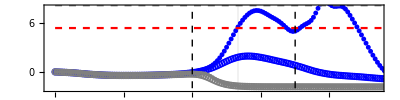

```mathematica
Show[ListPlot[{dat10,dat10b},Joined->False,
PlotStyle->{Blue,Blue,Gray},PlotMarkers->{{"●",5},{"○",6},{"○",6}},PlotRange->{{-2,NC+61},{-2.2,8}},GridLines->{{NC},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[7.206369005971784-1.828343796849751,{x,0,1100},PlotStyle->{Red,Dashed}],ListPlot[{dat10gr,dat10grb},PlotStyle->Gray,PlotMarkers->{{"●",3.8},{"○",6}},PlotLegends->Placed[{"",""},{0.05,0.46}]],Plot[10-1.828343796849751,{x,0,1100},PlotStyle->{Gray,Dashed}],Epilog->{Dashed,Black,Line[{{60,-2},{60,10}}],Line[{{105,-2},{105,10}}]},AspectRatio->0.25]
```

#### iii) a (Negativity)

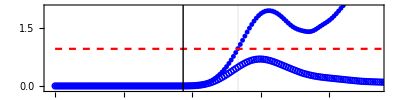

```mathematica
Show[ListPlot[{dat12,dat12b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"◇",6}},PlotRange->{{-2,NC+61},{-0.1,2.05}},GridLines->{{NC},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}](*,Plot[0,{x,0,1100},PlotStyle->{Black,Dashed}]*),Plot[0.96,{x,0,1100},PlotStyle->{Red,Dashed}],Epilog->{Black,Line[{{56,-3},{56,3}}]},AspectRatio->0.25]
```

#### iv) a (Chi)

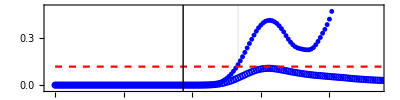

```mathematica
Show[ListPlot[{dat13,dat13b},Joined->False,
PlotStyle->{Blue,Blue},PlotMarkers->{{"●",5},{"○",6},{"◇",6}},PlotRange->{{-2,NC+61},{-0.03,0.5}},GridLines->{{NC},{}},Axes->False,GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}](*,Plot[0,{x,0,1100},PlotStyle->{Black,Dashed}]*),Plot[0.1178606006777,{x,0,1100},PlotStyle->{Red,Dashed}],Epilog->{Black,Line[{{56,-1},{56,1}}]},AspectRatio->0.25]
```

#### v) a (Negativity Correlation)

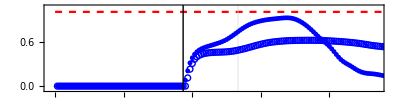

```mathematica
Show[ListPlot[{dat14,dat14b},Joined->False,
PlotStyle->{Blue,Blue,Blue,Darker[Green],Blue,Darker[Green]},PlotMarkers->{{"●",5},{"○",6},{"○",6},{"◇",6},{"◇",6}},PlotRange->{{-2,NC+61},{-0.05,1.07}},GridLines->{{NC},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[1,{x,0,1100},PlotStyle->{Red,Dashed}],Epilog->{Black,Line[{{56,-2},{56,2}}]}(*,Plot[0.9212480350262198,{x,0,1100},PlotStyle->{Black,Dashed}]*),AspectRatio->0.25]
```

#### Wigner function

```mathematica
(*Color for the Wigner function*)
FCo[t_]:=Piecewise[{{RGBColor[1,(2 t)^6,(2 t)^6],0<=t<=1/2},{RGBColor[(2-2 t)^6,(2-2 t)^6,1],1/2<t<=1}}]
```

```mathematica
datawigner1=Import["Data/WignerEx1_tau0.dat"];
datawigner2=Import["Data/WignerEx1_tau80.dat"];
datawigner3=Import["Data/WignerEx1_tau80_kappa.dat"];
datawigner4=Import["Data/WignerEx1_tar.dat"];
datawigner6=Import["Data/WignerEx2_tau80.dat"];
datawigner7=Import["Data/WignerEx2_tau80_kappa.dat"];
datawigner8=Import["Data/WignerEx2_tar.dat"];
```

```mathematica
fac=0.5/0.35;
wigner1=Show[ListDensityPlot[datawigner1,PlotRange->{{-1.0,1.0},{-1.0,1.0},All},Frame->True,LabelStyle->{Black,38},FrameTicks->{{{-1,0,1},None},{{-1,0,1},None}},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)]]
```

-Graphics-

```mathematica
wigner2=Show[ListDensityPlot[datawigner4,PlotRange->{{-1.0,1.0},{-1.0,1.0},All},Frame->True,LabelStyle->{Black,38},FrameTicks->{{{-1,0,1},None},{{-1,0,1},None}},FrameTicksStyle->{{FontOpacity->0,Automatic},{Automatic,Automatic}},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)]]
```

-Graphics-